```mathematica
R1=RegionPlot3D[2Sqrt[x^2+y^2]≤z≤2,{x,-1,1},{y,-1,1},{z,0,2},Axes->False, BoxRatios->{1,1,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.8]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,R1,P2,ViewPoint->{5,5,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

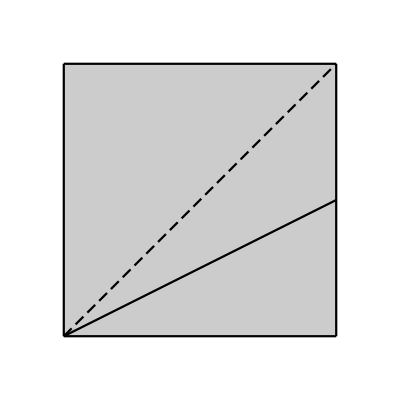

```mathematica
Quxian1=Plot[1,{x,0,1},Filling->Bottom,PlotStyle->Black];
Quxian2=ParametricPlot[{1,y},{y,0,1},PlotStyle->Black];
Quxian3=Plot[0,{x,0,1},PlotStyle->Black];
Quxian4=ParametricPlot[{0,y},{y,0,1},PlotStyle->Black];
Quxian5=Plot[x,{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]},Ticks->None];
Quxian6=Plot[0.5x,{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Black},Ticks->None];
Show[Quxian1,Quxian2,Quxian3,Quxian4,Quxian5,Quxian6,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.2/1.2,Frame->False,Ticks->None]
```

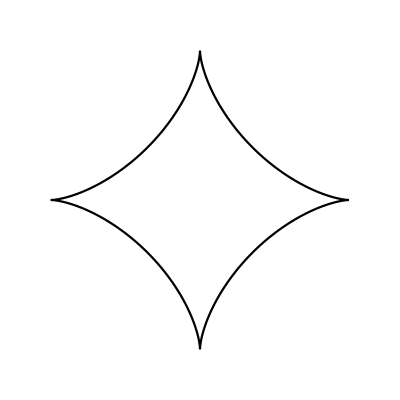

```mathematica
Quxian1=ParametricPlot[{Cos[theta]^3,Sin[theta]^3},{theta,0,2Pi},PlotStyle->Black];
Show[Quxian1,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.2/2.2,Frame->False,Ticks->None]
```

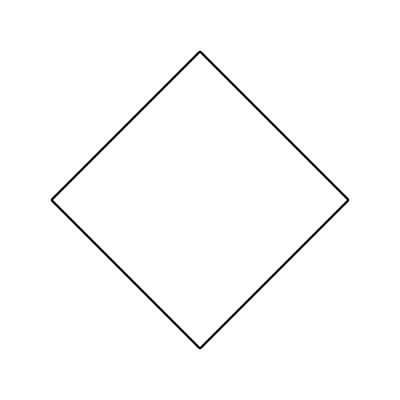

```mathematica
Quxian1=Plot[x-1,{x,0,1},PlotStyle->Black];
Quxian2=Plot[1-x,{x,1,0},PlotStyle->Black];
Quxian3=Plot[x+1,{x,0,-1},PlotStyle->Black];
Quxian4=Plot[-1-x,{x,-1,0},PlotStyle->Black];
Show[Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.2/2.2,Frame->False,Ticks->{{-1,1},{-1,1}}]
```

```mathematica
P2=ParametricPlot3D[{ Cos[theta], Sin[theta],z},{theta,0,Pi/2},{z,0,2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.8]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.0},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P2,ViewPoint->{5,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-